197.327

1.96628

/home/dmihaylov/Dudek_Ubuntu/Work/Kclus/GeneralFemtoStuff/CATS_TUTORIAL_2019/Mathematica/tab_txCBE.dat

/home/dmihaylov/Dudek_Ubuntu/Work/Kclus/GeneralFemtoStuff/CATS_TUTORIAL_2019/Mathematica/tab_txCoulombSame.dat

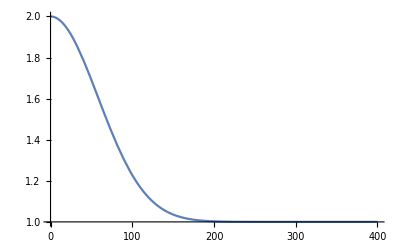

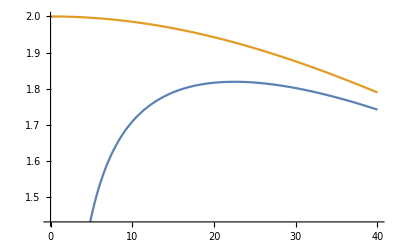

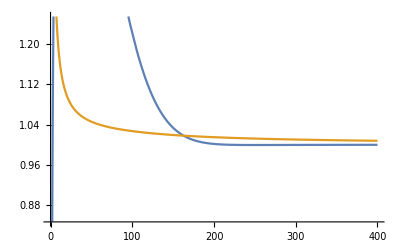

```mathematica
hbarc = 197.327
a=388/hbarc
Gamow[k_,Q1Q2_]:=(2π)/(a*k*Q1Q2)*1/(Exp[2π/(k*a*Q1Q2)]-1)
CoulombK[k_,Reff_,Q1Q2_]:=Gamow[k,Q1Q2]*(1+(8*Reff/hbarc)/(√π*a)*HypergeometricPFQ[{0.5,1},{1.5,1.5},-(2*Reff/hbarc*k)^2])
CBE[k_,Reff_]:=1+Exp[-(2*Reff/hbarc*k)^2]

txCBE=Table[{k,CBE[k,1.2]},{k,0.25,400.25,0.5}];
Export["/home/dmihaylov/Dudek_Ubuntu/Work/Kclus/GeneralFemtoStuff/CATS_TUTORIAL_2019/Mathematica/tab_txCBE.dat",txCBE]

txCoulombSame=Table[{k,CoulombK[k,1.2,1]},{k,0.25,400.25,0.5}];
Export["/home/dmihaylov/Dudek_Ubuntu/Work/Kclus/GeneralFemtoStuff/CATS_TUTORIAL_2019/Mathematica/tab_txCoulombSame.dat",txCoulombSame]


Plot[CBE[k,1.2],{k,0,400}]
Plot[{CBE[k,1.2]*CoulombK[k,1.2,1],CBE[k,1.2]},{k,0,40}]
Plot[{CBE[k,1.2]*CoulombK[k,1.2,1],CoulombK[k,1.2,-1]},{k,0,400}]
```